creatingintelligence.org

```mathematica
Module[{LEFTMARGIN=62,FONT="Inter Variable",TITLECOLOR=RGBColor["#BF616A"],TEXTCOLOR=RGBColor["#2E3440"]},(*Change LEFTMARGIN to whatever pixel/point value centers the 600px content*)SetOptions[EvaluationNotebook[],DockedCells->{Cell[BoxData[ToBoxes[Row[{Button["Export",Module[{nb=EvaluationNotebook[],cleanPath},cleanPath=FileNameJoin[{NotebookDirectory[nb],FileBaseName[NotebookFileName[nb]]}];
Export[cleanPath<>".pdf",nb];
Export[cleanPath<>".json",FromDFD[dataflow], "Circuit"]],Method->"Queued"]}]]],"DockedCell",Background->RGBColor["#EBCB8B"],CellMargins->{{0,0},{0,0}}]},(*Headers and Footers*)

PageHeaders->{{"","",""},{"","",""}},

PageFooters->{{"",Cell[TextData[CounterBox["Page"]]],""},{"",Cell[TextData[CounterBox["Page"]]],""}},

PageFooters->{{"",Cell[TextData[CounterBox["Page"]]],""},{"",Cell[TextData[CounterBox["Page"]]],""}},


PrintingOptions->{"PaperSize"->{510,680},(*{width,height} for Portrait*)"PrintingMargins"->{{0,0},{30,30}} (*left/right,bottom/top margins*)},(*Stylesheet overrides*)

StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],(*No header/footer lines*)Cell[StyleData["Header","Printout"],CellFrame->0],Cell[StyleData["Footer","Printout"],CellFrame->0],Cell[StyleData["Title","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,0}}],

Cell[StyleData["Subtitle","Printout"],FontColor->TITLECOLOR,FontSize->20,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{20,0}}],

Cell[StyleData["Section","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellFrame->False,PageBreakAbove->True,GroupPageBreakWithin->True,CellMargins->{{LEFTMARGIN,0},{20,10}}],Cell[StyleData["Subsection","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,10}}],Cell[StyleData["Subsubsection","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,10}}],Cell[StyleData["Text","Printout"],Hyphenation->True,
LineSpacing -> {1.4,0},FontColor->TEXTCOLOR,FontFamily->FONT,CellFrame->False,CellMargins->{{LEFTMARGIN,60},{7,7}}],Cell[StyleData["Code","Printout"],CellFrameMargins->{{20,0},{8,8}},PageWidth->670,CellMargins->{{LEFTMARGIN,30},{7,15}}],Cell[StyleData["Output","Printout"],PageWidth->660,CellMargins->{{LEFTMARGIN+20,0},{10,10}}],(*Hide Input cells in Printout*)Cell[StyleData["Input","Printout"],CellOpen->False,ShowCellBracket->False,CellMargins->{{LEFTMARGIN,0},{-2,-2}},CellElementSpacings->{"ClosedCellHeight"->0}]}]]];
```

# Semantic Similarity Index

## ARI measuring the similarity of two semantic fields

Store a dataset of 1.8M word associations (e.g. “ship”->”sail”) in hetero-associative memory. Retrieve the activation map for multiple words. Measure their similarity via the Adjusted Rand Index.

```mathematica
<< "Circuits.m"
```

```mathematica
c[Clear]; test[Clear];
```

### Hetero-associative memory circuit

```mathematica
{n, p} = {5000, 10};
```

```mathematica
dataflow = { 
		input[codec] [1] [], 
		input[codec] [2] [], 
		associator[] [11] [2, 1],
		output[] [] [11],
		_ -> {n, p}
	};
```

```mathematica
mem[Clear];
```

```mathematica
c = Circuit[dataflow]; c[Graph, ImageSize-> 220]
```

-Graphics-

### Import dataset

```mathematica
data = Import[ NotebookDirectory[] <>  "/data/word-associations.csv.zip", 
          "word-associations.csv"];
```

```mathematica
RandomSample[data, 10]
```

{dunes<->habitat,upped<->security,exercising<->flexibility,segregate<->distinguish,enthrallment<->spell,ambergris<->ocean,nature<->beach,self-referential<->self-aware,linearization<->straight,intermix<->splice}

```mathematica
Length[data]
```

1888505

### Train

```mathematica
c @@@ data;
```

### Adjusted Rand Index

```mathematica
ARI[A_List, B_List, dim_Integer] := 
N[(Length[Intersection[A,B]] - Length[A]*Length[B] / dim ) /
     (Min[Length[A], Length[B]] -  Length[A]*Length[B] / dim)]
```

```mathematica
similarity[x_, y_] := ARI[ c[x, Null], c[y, Null], n]
```

### Test

Retrieve activation map.

```mathematica
c[ "cat", Null]
```

Sequence[{19,23,32,43,61,66,74,80,116,126,129,145,152,188,220,241,296,325,342,343,370,377,385,388,419,454,456,467,495,500,530,534,546,548,560,584,589,610,619,633,675,687,688,693,697,708,710,732,754,758,773,787,794,800,803,807,837,864,881,925,973,986,1015,1037,1040,1045,1049,1052,1064,1069,1072,1077,1092,1109,1112,1115,1123,1150,1163,1169,1170,1188,1196,1200,1216,1219,1230,1277,1295,1302,1345,1376,1384,1390,1420,1444,1474,1483,1484,1506,1513,1519,1531,1555,1569,1574,1582,1592,1593,1598,1617,1640,1648,1672,1692,1723,1731,1787,1820,1825,1831,1835,1838,1864,1868,1888,1912,1916,1919,1922,1935,1950,1958,1983,1996,2008,2017,2018,2049,2070,2075,2088,2101,2102,2104,2166,2207,2221,2269,2286,2300,2333,2354,2395,2402,2406,2426,2434,2438,2463,2502,2503,2521,2559,2575,2590,2599,2600,2602,2617,2618,2647,2653,2693,2703,2749,2769,2790,2798,2809,2817,2825,2828,2830,2839,2858,2962,2967,2969,2970,3004,3032,3045,3050,3055,3130,3155,3163,3177,3187,3199,3207,3248,3250,3260,3263,3275,3277,3327,3329,3330,3336,3417,3418,3424,3476,3489,3508,3567,3580,3597,3612,3632,3635,3648,3674,3681,3702,3717,3735,3736,3742,3756,3798,3825,3838,3863,3884,3890,3913,3916,3931,3942,3943,3993,4010,4014,4015,4050,4114,4116,4168,4211,4232,4242,4250,4259,4267,4271,4273,4287,4297,4342,4382,4412,4438,4454,4476,4479,4481,4499,4520,4523,4531,4565,4571,4582,4584,4662,4703,4709,4714,4720,4732,4762,4767,4776,4780,4784,4792,4795,4820,4828,4831,4856,4858,4866,4868,4894,4917,4928,4956,4975,4982,4991}]

Measure semantic similarity via ARI:

```mathematica
similarity["ship", "boat"]
```

0.614402

```mathematica
similarity["ship", "cheese"]
```

-0.0248165

### Similarity Matrix

```mathematica
SimilarityMatrix[ items_List] := Module[ {simtable, xTicks, yTicks},
	
	simtable = Outer[ Round[similarity[##], 0.001]&, items, items]; 
	xTicks=Table[{i,Rotate[items[[i]],90 Degree], {0,0}},{i,Length[items]}];
	yTicks=Table[{i,items[[i]], {0,0}},{i,Length[items]}];
	
	MatrixPlot[simtable, 
		FrameTicks -> {{yTicks, None}, {None, xTicks}},
		FrameStyle -> Opacity[0],
		FrameTicksStyle -> Directive[Opacity[1],
		FontFamily -> "Inter Variable",
		FontSize->12]]
	]
```

```mathematica
items = {"cat",  "dog", "lion", "piano", 
      "electric", "power", "king", "queen", "liberty"};
```

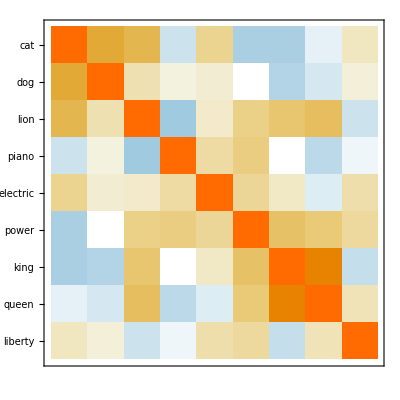

```mathematica
SimilarityMatrix[ items]
```

```mathematica
Export["similaritymatrix.png", ImagePad[Rasterize[%], 30, White]];
```